```mathematica
toPiecewise[wts_,x_]:=Piecewise[MapIndexed[{#1,x==#2[[1]]}&,wts]]
vRatePrior= {0.75,1.5,1.5,1.5,0.75,0};
vRatePosterior= {0.5,2,1.5,1,0.25,0};
vRatePosterior = vRatePosterior/Total@vRatePosterior;
vRatePrior = vRatePrior/Total@vRatePrior;
```

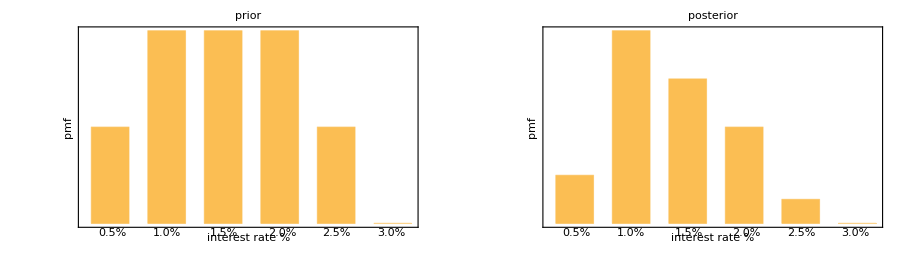

```mathematica
gPrior= BarChart[vRatePrior,BarSpacing->Large,FrameLabel->{"interest rate %", "pmf"},FrameTicks->{False,False},Frame->{True,True,False,False},PlotLabel->"prior",Epilog->{Text["0.5%",Scaled[{0.1,-.03}]],Text["1.0%",Scaled[{0.26,-.03}]],Text["1.5%",Scaled[{0.43,-.03}]],Text["2.0%",Scaled[{0.60,-.03}]],Text["2.5%",Scaled[{0.76,-.03}]],Text["3.0%",Scaled[{0.92,-.03}]]}];
gPosterior = BarChart[vRatePosterior,BarSpacing->Large,FrameLabel->{"interest rate %", "pmf"},FrameTicks->{False,False},PlotLabel->"posterior",Frame->{True,True,False,False},Epilog->{Text["0.5%",Scaled[{0.1,-.03}]],Text["1.0%",Scaled[{0.26,-.03}]],Text["1.5%",Scaled[{0.43,-.03}]],Text["2.0%",Scaled[{0.60,-.03}]],Text["2.5%",Scaled[{0.76,-.03}]],Text["3.0%",Scaled[{0.92,-.03}]]}];
Show[GraphicsRow[{gPrior,gPosterior}],ImageSize->900]
```

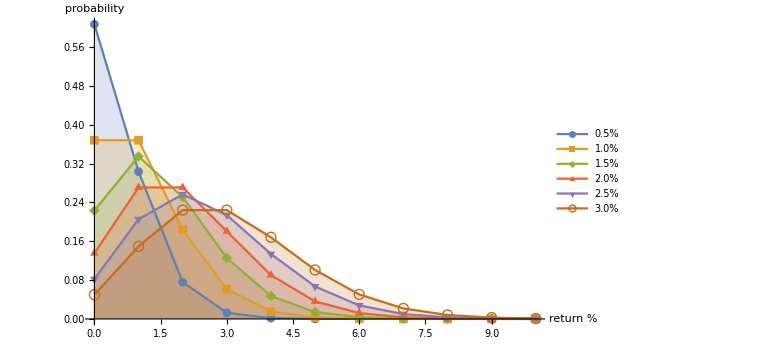

```mathematica
Show[DiscretePlot[Evaluate@Table[PDF[PoissonDistribution[λ],k],{λ,{0.5,1,1.5,2.0,2.5,3}}],{k,0,10},PlotRange->All,PlotMarkers->Automatic,Joined->True,PlotLegends->Placed[{"0.5%","1.0%","1.5%","2.0%","2.5%","3.0%"},Center],AxesLabel->{"return %","probability"},BaseStyle->{FontSize->14}],ImageSize->Large]
```

```mathematica
posteriorDistribution=ProbabilityDistribution[toPiecewise[vRatePosterior],{x,1,6,1}];
```

```mathematica
vLambda = {0.5,1.0,1.5,2.0,2.5,3.0};
priorPredictive[x_]:=Sum[PDF[PoissonDistribution[vLambda[[i]]],x]*vRatePrior[[i]],{i,1,6,1}]
```

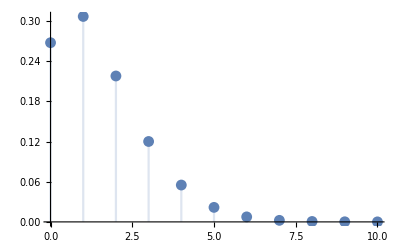

```mathematica
DiscretePlot[priorPredictive[x],{x,0,10,1}]
```